```mathematica
Monitor[Table[allGraphs6[k,"generators"]=FlatGenerators[allGraphs6[k,"colofour"]],{k,Sort[Keys[allGraphs6]]}],k];
```

```mathematica
FullBaseCoeff6[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs6[#,"colofour"]&,allGraphs6AtomKeys]}],CompareSymbols]}]
```

```mathematica
Sort[Table[var,{var,Map[allGraphs6[#,"colofour"]&,allGraphs6AtomKeys]}],CompareSymbols]
```

```mathematica
{v1x2x3x4x6,v1x2x3x46,v1x2x34x6,v1x2x36x4,v1x23x4x6,v1x24x3x6,v1x26x3x4,v12x3x4x6,v13x2x4x6,v14x2x3x6,v16x2x3x4,v1x23x46,v1x24x36,v1x26x34,v12x3x46,v12x34x6,v12x36x4,v13x2x46,v13x24x6,v13x26x4,v14x2x36,v14x23x6,v14x26x3,v16x2x34,v16x23x4,v16x24x3,v1x2x346,v1x234x6,v1x236x4,v1x246x3,v123x4x6,v124x3x6,v126x3x4,v134x2x6,v136x2x4,v146x2x3,v12x346,v123x46,v124x36,v126x34,v13x246,v134x26,v136x24,v14x236,v146x23,v16x234,v1x2346,v1234x6,v1236x4,v1246x3,v1346x2,v12346}
```

```mathematica
EmptyBaseCoeff6[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs6[#,"colofourrealnull"]&,allGraphs6NullAtomKeys]}],CompareSymbols]}]
```

```mathematica
FullBaseCoeff6[allGraphs6[0,"colofour"]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
theGens6=Sort[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&Length[ListofVars[allGraphs6[#,"generators"]]]==1&],CompareSymbols[First[allGraphs6[#1,"generators"]],First[allGraphs6[#2,"generators"]]]&];
```

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"v"->prefix]]
```

```mathematica
repGen6=First[Solve[Table[ChangeSymbol[First[allGraphs6[k,"generators"]],"g"]==allGraphs6[k,"colofour"],{k,theGens6}],Table[allGraphs6[m,"colofour"],{m,allGraphs6AtomKeys}]]];
```

```mathematica
Monitor[Table[allGraphs6[k,"genfour"]=Simplify[allGraphs6[k,"colofour"]/.repGen6],{k,Sort[Keys[allGraphs6]]}],k];
```

```mathematica
DocValue6[key_]:=With[
{rep=Join[
Table[ChangeSymbol[k,"g"]->Style[ChangeSymbol[k,"g"],Red,Bold],{k,FlatGenerators[allGraphs6[key,"generators"]]}],
Table[k->Style[k,Red],{k,FlatGenerators[allGraphs6[key,"generators"]]}]]},
Table[allGraphs6[key,code]/.rep,{code,{"generators","genfour","colofour"}}]
]
```

```mathematica
GenIndices6[key_]:=Block[{gens=Map[ChangeSymbol[#,"g"]&,FlatGenerators[allGraphs6[key,"generators"]]],gens2=Map[ChangeSymbol[#,"v"]&,FlatGenerators[allGraphs6[key,"generators"]]],genForm=allGraphs6[key,"genfour"],
genColor=allGraphs6[key,"colofour"]},
With[{a=Table[Coefficient[genForm,var],{var,gens}],b=Table[Coefficient[genColor,var],{var,gens2}]},
{
a,
b,
a==b
}
]
]
```

```mathematica
MobGen[k_]:=With[{
m=MobiusGraph6[K6Key,allGraphs6],
gen=Map[ChangeSymbol[#,"n"]&,allGraphs6[k,"generators"]],
full=Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs6[k,"colofour"]]]
},
Graph[VertexList[m],EdgeList[m],VertexStyle->Table[v->Blue,{v,gen}],VertexLabels->Table[v->SymbolName[v],{v,full}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
MobGen[3]
```

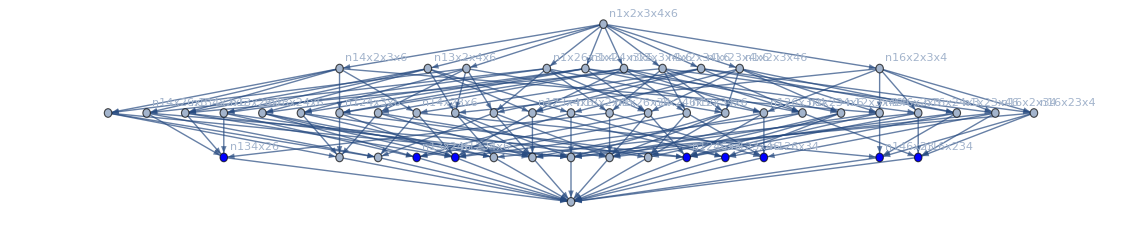

```mathematica
ChangeSymbolEmpty[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"g"->prefix]]
```

```mathematica
MobGen2[k_]:=With[{
m=MobiusGraph6[K6Key,allGraphs6],
gen=Sort[Map[ChangeSymbolEmpty[#,"n"]&,ListofVars[allGraphs6[k,"genfour"]]],CompareSymbols],
full=Sort[Map[ChangeSymbol[#,"n"]&,ListofVars[allGraphs6[k,"colofour"]]],CompareSymbols]
},
Labeled[
Graph[VertexList[m],EdgeList[m],VertexStyle->Table[v->Blue,{v,gen}],VertexLabels->Table[v->SymbolName[v],{v,full}],GraphLayout->"LayeredDigraphEmbedding"],
ToString[gen]==ToString[full]
]
]
```

```mathematica
MobGen2[1]
```

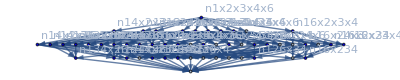
```mathematica
-Graphics-True
```

```mathematica
XPower[sym_]:=x^(1+StringCount[SymbolName[sym],"x"])
```

```mathematica
genRep6=Table[allGraphs6[k,"genfour"]->ChromaticPolynomial[allGraphs6[k,"graph"],x],{k,theGens6}]
```

```mathematica
{g1x2x3x4x6->24 x-60 x^2+36 x^3-10 x^4+x^6,g1x2x3x46->18 x-39 x^2+29 x^3-9 x^4+x^6,g1x2x34x6->18 x-39 x^2+29 x^3-9 x^4+x^6,g1x2x36x4->18 x-39 x^2+29 x^3-9 x^4+x^6,g1x23x4x6->18 x-39 x^2+29 x^3-9 x^4+x^6,g1x24x3x6->18 x-39 x^2+29 x^3-9 x^4+x^6,g1x26x3x4->18 x-39 x^2+29 x^3-9 x^4+x^6,g12x3x4x6->18 x-39 x^2+29 x^3-9 x^4+x^6,g13x2x4x6->18 x-39 x^2+29 x^3-9 x^4+x^6,g14x2x3x6->18 x-39 x^2+29 x^3-9 x^4+x^6,g16x2x3x4->18 x-39 x^2+29 x^3-9 x^4+x^6,g1x23x46->14 x-31 x^2+24 x^3-8 x^4+x^6,g1x24x36->14 x-31 x^2+24 x^3-8 x^4+x^6,g1x26x34->14 x-31 x^2+24 x^3-8 x^4+x^6,g12x3x46->14 x-31 x^2+24 x^3-8 x^4+x^6,g12x34x6->14 x-31 x^2+24 x^3-8 x^4+x^6,g12x36x4->14 x-31 x^2+24 x^3-8 x^4+x^6,g13x2x46->14 x-31 x^2+24 x^3-8 x^4+x^6,g13x24x6->14 x-31 x^2+24 x^3-8 x^4+x^6,g13x26x4->14 x-31 x^2+24 x^3-8 x^4+x^6,g14x2x36->14 x-31 x^2+24 x^3-8 x^4+x^6,g14x23x6->14 x-31 x^2+24 x^3-8 x^4+x^6,g14x26x3->14 x-31 x^2+24 x^3-8 x^4+x^6,g16x2x34->14 x-31 x^2+24 x^3-8 x^4+x^6,g16x23x4->14 x-31 x^2+24 x^3-8 x^4+x^6,g16x24x3->14 x-31 x^2+24 x^3-8 x^4+x^6,g1x2x346->8 x-20 x^2+18 x^3-7 x^4+x^6,g1x234x6->8 x-20 x^2+18 x^3-7 x^4+x^6,g1x236x4->8 x-20 x^2+18 x^3-7 x^4+x^6,g1x246x3->8 x-20 x^2+18 x^3-7 x^4+x^6,g123x4x6->8 x-20 x^2+18 x^3-7 x^4+x^6,g124x3x6->8 x-20 x^2+18 x^3-7 x^4+x^6,g126x3x4->8 x-20 x^2+18 x^3-7 x^4+x^6,g134x2x6->8 x-20 x^2+18 x^3-7 x^4+x^6,g136x2x4->8 x-20 x^2+18 x^3-7 x^4+x^6,g146x2x3->8 x-20 x^2+18 x^3-7 x^4+x^6,g12x346->7 x-17 x^2+16 x^3-6 x^4+x^6,g123x46->7 x-17 x^2+16 x^3-6 x^4+x^6,g124x36->7 x-17 x^2+16 x^3-6 x^4+x^6,g126x34->7 x-17 x^2+16 x^3-6 x^4+x^6,g13x246->7 x-17 x^2+16 x^3-6 x^4+x^6,g134x26->7 x-17 x^2+16 x^3-6 x^4+x^6,g136x24->7 x-17 x^2+16 x^3-6 x^4+x^6,g14x236->7 x-17 x^2+16 x^3-6 x^4+x^6,g146x23->7 x-17 x^2+16 x^3-6 x^4+x^6,g16x234->7 x-17 x^2+16 x^3-6 x^4+x^6,g1x2346->x-4 x^2+6 x^3-4 x^4+x^6,g1234x6->x-4 x^2+6 x^3-4 x^4+x^6,g1236x4->x-4 x^2+6 x^3-4 x^4+x^6,g1246x3->x-4 x^2+6 x^3-4 x^4+x^6,g1346x2->x-4 x^2+6 x^3-4 x^4+x^6,g12346->x^6}
```

```mathematica
Table[CoefficientList[ChromaticPolynomial[allGraphs6[k,"graph"],x],x],{k,theGens6}]//MatrixForm
```

```mathematica
({{0, 24, -60, 36, -10, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 18, -39, 29, -9, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 14, -31, 24, -8, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 8, -20, 18, -7, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 7, -17, 16, -6, 1}, {0, 1, -4, 6, -4, 1}, {0, 1, -4, 6, -4, 1}, {0, 1, -4, 6, -4, 1}, {0, 1, -4, 6, -4, 1}, {0, 1, -4, 6, -4, 1}, {0, 0, 0, 0, 0, 1}})
```

```mathematica
fullRep6=Table[allGraphs6[k,"colofour"]->ChromaticPolynomial[allGraphs6[k,"graph"],x],{k,allGraphs6AtomKeys}]
```

```mathematica
{v1x2x3x4x6->24 x-60 x^2+36 x^3-10 x^4+x^6,v1x2x3x46->-6 x+11 x^2-6 x^3+x^4,v1x2x36x4->-6 x+11 x^2-6 x^3+x^4,v1x2x34x6->-6 x+11 x^2-6 x^3+x^4,v1x2x346->2 x-3 x^2+x^3,v1x26x3x4->-6 x+11 x^2-6 x^3+x^4,v1x26x34->2 x-3 x^2+x^3,v1x24x3x6->-6 x+11 x^2-6 x^3+x^4,v1x24x36->2 x-3 x^2+x^3,v1x246x3->2 x-3 x^2+x^3,v1x23x4x6->-6 x+11 x^2-6 x^3+x^4,v1x23x46->2 x-3 x^2+x^3,v1x236x4->2 x-3 x^2+x^3,v1x234x6->2 x-3 x^2+x^3,v1x2346->-x+x^2,v16x2x3x4->-6 x+11 x^2-6 x^3+x^4,v16x2x34->2 x-3 x^2+x^3,v16x24x3->2 x-3 x^2+x^3,v16x23x4->2 x-3 x^2+x^3,v16x234->-x+x^2,v14x2x3x6->-6 x+11 x^2-6 x^3+x^4,v14x2x36->2 x-3 x^2+x^3,v14x26x3->2 x-3 x^2+x^3,v14x23x6->2 x-3 x^2+x^3,v14x236->-x+x^2,v146x2x3->2 x-3 x^2+x^3,v146x23->-x+x^2,v13x2x4x6->-6 x+11 x^2-6 x^3+x^4,v13x2x46->2 x-3 x^2+x^3,v13x26x4->2 x-3 x^2+x^3,v13x24x6->2 x-3 x^2+x^3,v13x246->-x+x^2,v136x2x4->2 x-3 x^2+x^3,v136x24->-x+x^2,v134x2x6->2 x-3 x^2+x^3,v134x26->-x+x^2,v1346x2->-x+x^2,v12x3x4x6->-6 x+11 x^2-6 x^3+x^4,v12x3x46->2 x-3 x^2+x^3,v12x36x4->2 x-3 x^2+x^3,v12x34x6->2 x-3 x^2+x^3,v12x346->-x+x^2,v126x3x4->2 x-3 x^2+x^3,v126x34->-x+x^2,v124x3x6->2 x-3 x^2+x^3,v124x36->-x+x^2,v1246x3->-x+x^2,v123x4x6->2 x-3 x^2+x^3,v123x46->-x+x^2,v1236x4->-x+x^2,v1234x6->-x+x^2,v12346->x}
```

```mathematica
MobGen3[k_]:=With[{
m=MobiusGraph6[K6Key,allGraphs6],
gen=allGraphs6[k,"genfour"],
full=allGraphs6[k,"colofour"]
},
Simplify[{ChromaticPolynomial[allGraphs6[k,"graph"],x], gen,full,(gen/.genRep6),(full/.fullRep6)}]
]
```

```mathematica
MobGen3[1]
```

```mathematica
{(-1+x) x^4,g1234x6+g1236x4-g123x4x6+g124x36-g124x3x6+g126x34-g126x3x4-g12x34x6-g12x36x4+2 g12x3x4x6+g134x26-g134x2x6+g136x24-g136x2x4-g13x24x6-g13x26x4+2 g13x2x4x6+g14x236-g14x23x6-g14x26x3-g14x2x36+2 g14x2x3x6+g16x234-g16x23x4-g16x24x3-g16x2x34+2 g16x2x3x4-g1x234x6-g1x236x4+2 g1x23x4x6-g1x24x36+2 g1x24x3x6-g1x26x34+2 g1x26x3x4+2 g1x2x34x6+2 g1x2x36x4-6 g1x2x3x4x6,v1234x6+v1236x4+v123x4x6+v124x36+v124x3x6+v126x34+v126x3x4+v12x34x6+v12x36x4+v12x3x4x6+v134x26+v134x2x6+v136x24+v136x2x4+v13x24x6+v13x26x4+v13x2x4x6+v14x236+v14x23x6+v14x26x3+v14x2x36+v14x2x3x6+v16x234+v16x23x4+v16x24x3+v16x2x34+v16x2x3x4+v1x234x6+v1x236x4+v1x23x4x6+v1x24x36+v1x24x3x6+v1x26x34+v1x26x3x4+v1x2x34x6+v1x2x36x4+v1x2x3x4x6,(-1+x) x^4,(-1+x) x^4}
```

```mathematica
GenIndices6[271]
```

{{1,1,1,1,1},{1,1,1,1,1},True}

```mathematica
Table[ShowGraph[allGraphs6,k]->{Length[ListofVars[allGraphs6[k,"colofour"]]],Length[ListofVars[allGraphs6[k,"genfour"]]],Length[FlatGenerators[allGraphs6[k,"colofour"]]]},{k,Take[Keys[allGraphs6],20]}]
```

```mathematica
{-Graphics-0->{62,1,1},-Graphics-19683->{37,37,8},-Graphics-26244->{27,10,4},-Graphics-28431->{20,3,2},-Graphics-29160->{16,1,1},-Graphics-29403->{10,10,4},-Graphics-29484->{7,3,2},-Graphics-29611->{6,1,1},-Graphics-29620->{3,3,2},-Graphics-29623->{2,1,1},-Graphics-29624->{1,1,1},-Graphics-29626->{1,2,1},-Graphics-29627->{1,2,1},-Graphics-29621->{2,1,1},-Graphics-29629->{2,4,1},-Graphics-29633->{1,2,1},-Graphics-29637->{1,6,1},-Graphics-29614->{3,3,2},-Graphics-29616->{2,1,1},-Graphics-29617->{2,4,1}}
```

```mathematica
Table[ShowGraph[allGraphs6,k]->GenIndices6[k],{k,Take[Keys[allGraphs6],20]}]
```

```mathematica
{-Graphics-0->{{1},{1},True},-Graphics-19683->{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},True},-Graphics-26244->{{1,1,1,1},{1,1,1,1},True},-Graphics-28431->{{1,1},{1,1},True},-Graphics-29160->{{1},{1},True},-Graphics-29403->{{1,1,1,1},{1,1,1,1},True},-Graphics-29484->{{1,1},{1,1},True},-Graphics-29611->{{1},{1},True},-Graphics-29620->{{1,1},{1,1},True},-Graphics-29623->{{1},{1},True},-Graphics-29624->{{1},{1},True},-Graphics-29626->{{1},{1},True},-Graphics-29627->{{1},{1},True},-Graphics-29621->{{1},{1},True},-Graphics-29629->{{1},{1},True},-Graphics-29633->{{1},{1},True},-Graphics-29637->{{1},{1},True},-Graphics-29614->{{1,1},{1,1},True},-Graphics-29616->{{1},{1},True},-Graphics-29617->{{1},{1},True}}
```

```mathematica
{-Graphics-0->{{1},{1},True},-Graphics-263->{{1,1,1,1},{1,1,1,1},True},-Graphics-326->{{1,1},{1,1},True},-Graphics-361->{{1},{1},True},-Graphics-360->{{1,1},{1,1},True},-Graphics-363->{{1},{1},True},-Graphics-366->{{1},{1},True},-Graphics-366->{{1},{1},True},-Graphics-367->{{1},{1},True},-Graphics-361->{{1},{1},True},-Graphics-369->{{1},{1},True},-Graphics-373->{{1},{1},True},-Graphics-377->{{1},{1},True},-Graphics-366->{{1,1},{1,1},True},-Graphics-366->{{1},{1},True},-Graphics-367->{{1},{1},True},-Graphics-362->{{1,1},{1,1},True},-Graphics-363->{{1},{1},True},-Graphics-382->{{1},{1},True},-Graphics-391->{{1},{1},True}}
```

```mathematica
{-Graphics-0->{{1},{1},True},-Graphics-263->{{1,1,1,1},{1,1,1,1},True},-Graphics-326->{{1,1},{1,1},True},-Graphics-361->{{1},{1},True},-Graphics-360->{{1,1},{1,1},True},-Graphics-363->{{1},{1},True},-Graphics-366->{{1},{1},True},-Graphics-366->{{1},{1},True},-Graphics-367->{{1},{1},True},-Graphics-361->{{1},{1},True},-Graphics-369->{{1},{1},True},-Graphics-373->{{1},{1},True},-Graphics-377->{{1},{1},True},-Graphics-366->{{1,1},{1,1},True},-Graphics-366->{{1},{1},True},-Graphics-367->{{1},{1},True},-Graphics-362->{{1,1},{1,1},True},-Graphics-363->{{1},{1},True},-Graphics-382->{{1},{1},True},-Graphics-391->{{1},{1},True}}
```

```mathematica
Table[ShowGraph[allGraphs6,k]->DocValue6[k],{k,Take[Keys[allGraphs6],10]}]
```

```mathematica
{-Graphics-0->{{v12346},g12346,v1234x6+v1236x4+v123x46+v123x4x6+v1246x3+v124x36+v124x3x6+v126x34+v126x3x4+v12x346+v12x34x6+v12x36x4+v12x3x46+v12x3x4x6+v1346x2+v134x26+v134x2x6+v136x24+v136x2x4+v13x246+v13x24x6+v13x26x4+v13x2x46+v13x2x4x6+v146x23+v146x2x3+v14x236+v14x23x6+v14x26x3+v14x2x36+v14x2x3x6+v16x234+v16x23x4+v16x24x3+v16x2x34+v16x2x3x4+v1x2346+v1x234x6+v1x236x4+v1x23x46+v1x23x4x6+v1x246x3+v1x24x36+v1x24x3x6+v1x26x34+v1x26x3x4+v1x2x346+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v12346},-Graphics-19683->{{v1x2346,v16x234,v14x236,v146x23,v13x246,v136x24,v134x26,v1346x2},-g134x2x6-g136x2x4-g13x24x6-g13x26x4-g13x2x46+2 g13x2x4x6-g146x2x3-g14x23x6-g14x26x3-g14x2x36+2 g14x2x3x6-g16x23x4-g16x24x3-g16x2x34+2 g16x2x3x4-g1x234x6-g1x236x4-g1x23x46+2 g1x23x4x6-g1x246x3-g1x24x36+2 g1x24x3x6-g1x26x34+2 g1x26x3x4-g1x2x346+2 g1x2x34x6+2 g1x2x36x4+2 g1x2x3x46-6 g1x2x3x4x6+g1346x2+g134x26+g136x24+g13x246+g146x23+g14x236+g16x234+g1x2346,v134x2x6+v136x2x4+v13x24x6+v13x26x4+v13x2x46+v13x2x4x6+v146x2x3+v14x23x6+v14x26x3+v14x2x36+v14x2x3x6+v16x23x4+v16x24x3+v16x2x34+v16x2x3x4+v1x234x6+v1x236x4+v1x23x46+v1x23x4x6+v1x246x3+v1x24x36+v1x24x3x6+v1x26x34+v1x26x3x4+v1x2x346+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v1346x2+v134x26+v136x24+v13x246+v146x23+v14x236+v16x234+v1x2346},-Graphics-26244->{{v1x2346,v16x234,v14x236,v146x23},-g14x23x6-g16x23x4-g1x234x6-g1x236x4-g1x23x46+2 g1x23x4x6+g146x23+g14x236+g16x234+g1x2346,v146x2x3+v14x23x6+v14x26x3+v14x2x36+v14x2x3x6+v16x23x4+v16x24x3+v16x2x34+v16x2x3x4+v1x234x6+v1x236x4+v1x23x46+v1x23x4x6+v1x246x3+v1x24x36+v1x24x3x6+v1x26x34+v1x26x3x4+v1x2x346+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v146x23+v14x236+v16x234+v1x2346},-Graphics-28431->{{v1x2346,v16x234},-g1x234x6+g16x234+g1x2346,v16x23x4+v16x24x3+v16x2x34+v16x2x3x4+v1x234x6+v1x236x4+v1x23x46+v1x23x4x6+v1x246x3+v1x24x36+v1x24x3x6+v1x26x34+v1x26x3x4+v1x2x346+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v16x234+v1x2346},-Graphics-29160->{{v1x2346},g1x2346,v1x234x6+v1x236x4+v1x23x46+v1x23x4x6+v1x246x3+v1x24x36+v1x24x3x6+v1x26x34+v1x26x3x4+v1x2x346+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v1x2346},-Graphics-29403->{{v1x2x346,v1x26x34,v1x24x36,v1x246x3},-g1x24x3x6-g1x26x3x4-g1x2x34x6-g1x2x36x4-g1x2x3x46+2 g1x2x3x4x6+g1x246x3+g1x24x36+g1x26x34+g1x2x346,v1x24x3x6+v1x26x3x4+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v1x246x3+v1x24x36+v1x26x34+v1x2x346},-Graphics-29484->{{v1x2x346,v1x26x34},-g1x2x34x6+g1x26x34+g1x2x346,v1x26x3x4+v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v1x26x34+v1x2x346},-Graphics-29611->{{v1x2x346},g1x2x346,v1x2x34x6+v1x2x36x4+v1x2x3x46+v1x2x3x4x6+v1x2x346},-Graphics-29620->{{v1x2x3x46,v1x2x36x4},-g1x2x3x4x6+g1x2x36x4+g1x2x3x46,v1x2x3x4x6+v1x2x36x4+v1x2x3x46},-Graphics-29623->{{v1x2x3x46},g1x2x3x46,v1x2x3x4x6+v1x2x3x46}}
```

```mathematica
{-Graphics-0->{{v1236},g1236,v123x6+v126x3+v12x36+v12x3x6+v136x2+v13x26+v13x2x6+v16x23+v16x2x3+v1x236+v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v1236},-Graphics-263->{{v1x236,v16x23,v13x26,v136x2},-g13x2x6-g16x2x3-g1x23x6-g1x26x3-g1x2x36+2 g1x2x3x6+g136x2+g13x26+g16x23+g1x236,v13x2x6+v16x2x3+v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v136x2+v13x26+v16x23+v1x236},-Graphics-326->{{v1x236,v16x23},-g1x23x6+g16x23+g1x236,v16x2x3+v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v16x23+v1x236},-Graphics-361->{{v1x236},g1x236,v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v1x236},-Graphics-360->{{v1x2x36,v1x26x3},-g1x2x3x6+g1x26x3+g1x2x36,v1x2x3x6+v1x26x3+v1x2x36},-Graphics-363->{{v1x2x36},g1x2x36,v1x2x3x6+v1x2x36},-Graphics-366->{{v1x2x3x6},g1x2x3x6,v1x2x3x6},-Graphics-366->{{v1x2x36},-g1x2x3x6+g1x2x36,v1x2x36},-Graphics-367->{{v1x26x3},-g1x2x3x6+g1x26x3,v1x26x3},-Graphics-361->{{v1x26x3},g1x26x3,v1x2x3x6+v1x26x3}}
```

```mathematica
{-Graphics-0->{{v1236},g1236,v123x6+v126x3+v12x36+v12x3x6+v136x2+v13x26+v13x2x6+v16x23+v16x2x3+v1x236+v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v1236},-Graphics-263->{{v1x236,v16x23,v13x26,v136x2},-g13x2x6-g16x2x3-g1x23x6-g1x26x3-g1x2x36+2 g1x2x3x6+g136x2+g13x26+g16x23+g1x236,v13x2x6+v16x2x3+v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v136x2+v13x26+v16x23+v1x236},-Graphics-326->{{v1x236,v16x23},-g1x23x6+g16x23+g1x236,v16x2x3+v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v16x23+v1x236},-Graphics-361->{{v1x236},g1x236,v1x23x6+v1x26x3+v1x2x36+v1x2x3x6+v1x236},-Graphics-360->{{v1x2x36,v1x26x3},-g1x2x3x6+g1x26x3+g1x2x36,v1x2x3x6+v1x26x3+v1x2x36},-Graphics-363->{{v1x2x36},g1x2x36,v1x2x3x6+v1x2x36},-Graphics-366->{{v1x2x3x6},g1x2x3x6,v1x2x3x6},-Graphics-366->{{v1x2x36},-g1x2x3x6+g1x2x36,v1x2x36},-Graphics-367->{{v1x26x3},-g1x2x3x6+g1x26x3,v1x26x3},-Graphics-361->{{v1x26x3},g1x26x3,v1x2x3x6+v1x26x3}}
```

```mathematica
GenBaseCoeff[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Table[ChangeSymbol[First[allGraphs6[k,"generators"]],"g"],{k,theGens6}]}],CompareSymbols]}]
```

```mathematica
Table[With[{c=EmptyBaseCoeff6[allGraphs6[k,"colofourrealnull"]]},{Min[c],Max[c]}],{k,theGens6}]//Tally
```

```mathematica
{{{-6,24},1},{{-6,18},10},{{-4,14},16},{{-4,8},10},{{-3,7},10},{{-1,1},6},{{0,1},1}}
```

```mathematica
{{{-6,2},1},{{-6,2},6},{{-3,1},3},{{-1,1},6},{{0,1},1}}
```

```mathematica
{{{-6,2},1},{{-6,2},6},{{-3,1},3},{{-1,1},6},{{0,1},1}}
```

```mathematica
{{{-120,26},1},{{-96,26},16},{{-78,18},66},{{-66,18},20},{{-66,16},16},{{-66,16},60},{{-16,8},16},{{-31,7},10},{{-16,7},16},{{-1,1},6},{{0,1},1}}
```

```mathematica
{{{-120,26},1},{{-96,26},16},{{-78,18},66},{{-66,18},20},{{-66,16},16},{{-66,16},60},{{-16,8},16},{{-31,7},10},{{-16,7},16},{{-1,1},6},{{0,1},1}}
```

```mathematica
{{{-120,26},1},{{-96,26},16},{{-78,18},66},{{-66,18},20},{{-66,16},16},{{-66,16},60},{{-16,8},16},{{-31,7},10},{{-16,7},16},{{-1,1},6},{{0,1},1}}
```

```mathematica
{{{-120,26},1},{{-96,26},16},{{-78,18},66},{{-66,18},20},{{-66,16},16},{{-66,16},60},{{-16,8},16},{{-31,7},10},{{-16,7},16},{{-1,1},6},{{0,1},1}}
```

```mathematica
EmptyBaseCoeff6[allGraphs6[1,"colofourrealnull"]]
```

{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
theGens6Comp=Table[FindComplement[k,allGraphs6],{k,theGens6}]
```

```mathematica
{0,1,9,3,243,81,27,19683,6661,2187,729,244,84,36,19684,19692,19686,6662,6642,6688,2190,2430,2214,738,972,810,13,333,273,109,26487,21961,20439,8767,7293,2917,19696,26488,21964,20448,6670,8784,7374,2460,3160,1062,364,28764,27246,22708,9490,29624}
```

```mathematica
SummarizeGenerators[k_]:=Block[{gen=BaseGenerators[allGraphs6[k,"colofour"]],keys},
keys=Keys[gen];
Table[{kk,Length[gen[kk]]},{kk,Sort[keys]}]]
```

```mathematica
SummarizeGenerators[1]
```

{{2,8}}

```mathematica
{{2,6}}
```

```mathematica
{{2,6}}
```

```mathematica
Table[SummarizeGenerators[k],{k,theGens6Comp}]
```

```mathematica
{{{1,1}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{2,4}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,9}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{6,1}}}
```

```mathematica
{{{1,1}},{{2,6}},{{2,6}},{{2,6}},{{2,6}},{{2,6}},{{2,6}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{6,1}}}
```

```mathematica
{{{1,1}},{{2,6}},{{2,6}},{{2,6}},{{2,6}},{{2,6}},{{2,6}},{{2,2}},{{2,2}},{{2,2}},{{3,3}},{{3,3}},{{3,3}},{{3,3}},{{6,1}}}
```

```mathematica
Multicolumn[Table[Framed[Labeled[{
ShowGraph[allGraphs6,k],
ShowGraph[allGraphs6,FindComplement[k,allGraphs6]]
},SymbolToLabel2[allGraphs6[k,"generators"]//First,6],Top]],{k,theGens6}],8,Appearance->"Horizontal"]
```

```mathematica
{{{-Graphics-29624,-Graphics-0}OverHat[1], {-Graphics-29623,-Graphics-1}"46", {-Graphics-29616,-Graphics-9}"34", {-Graphics-29621,-Graphics-3}"36", {-Graphics-29281,-Graphics-243}"23", {-Graphics-29443,-Graphics-81}"24", {-Graphics-29497,-Graphics-27}"26", {-Graphics-9841,-Graphics-19683}"12"}, {{-Graphics-22963,-Graphics-6661}"13", {-Graphics-27337,-Graphics-2187}"14", {-Graphics-28796,-Graphics-729}"16", {-Graphics-29280,-Graphics-244}"23""♁""46", {-Graphics-29440,-Graphics-84}"24""♁""36", {-Graphics-29488,-Graphics-36}"26""♁""34", {-Graphics-9840,-Graphics-19684}"12""♁""46", {-Graphics-9832,-Graphics-19692}"12""♁""34"}, {{-Graphics-9838,-Graphics-19686}"12""♁""36", {-Graphics-22962,-Graphics-6662}"13""♁""46", {-Graphics-22882,-Graphics-6642}"13""♁""24", {-Graphics-22936,-Graphics-6688}"13""♁""26", {-Graphics-27334,-Graphics-2190}"14""♁""36", {-Graphics-27094,-Graphics-2430}"14""♁""23", {-Graphics-27310,-Graphics-2214}"14""♁""26", {-Graphics-28786,-Graphics-738}"16""♁""34"}, {{-Graphics-28662,-Graphics-972}"16""♁""23", {-Graphics-28714,-Graphics-810}"16""♁""24", {-Graphics-29611,-Graphics-13}"346", {-Graphics-29191,-Graphics-333}"234", {-Graphics-29261,-Graphics-273}"236", {-Graphics-29416,-Graphics-109}"246", {-Graphics-3037,-Graphics-26487}"123", {-Graphics-7673,-Graphics-21961}"124"}, {{-Graphics-9086,-Graphics-20439}"126", {-Graphics-20767,-Graphics-8767}"134", {-Graphics-22231,-Graphics-7293}"136", {-Graphics-26607,-Graphics-2917}"146", {-Graphics-9828,-Graphics-19696}"12""♁""346", {-Graphics-3036,-Graphics-26488}"123""♁""46", {-Graphics-7670,-Graphics-21964}"124""♁""36", {-Graphics-9076,-Graphics-20448}"126""♁""34"}, {{-Graphics-22864,-Graphics-6670}"13""♁""246", {-Graphics-20740,-Graphics-8784}"134""♁""26", {-Graphics-22160,-Graphics-7374}"136""♁""24", {-Graphics-27064,-Graphics-2460}"14""♁""236", {-Graphics-26364,-Graphics-3160}"146""♁""23", {-Graphics-28462,-Graphics-1062}"16""♁""234", {-Graphics-29160,-Graphics-364}"2346", {-Graphics-760,-Graphics-28764}"1234"}, {{-Graphics-2278,-Graphics-27246}"1236", {-Graphics-6816,-Graphics-22708}"1246", {-Graphics-20034,-Graphics-9490}"1346", {-Graphics-0,-Graphics-29624}OverHat[0], "", "", "", ""}}
```

```mathematica
{{{-Graphics-366,-Graphics-0}OverHat[1], {-Graphics-363,-Graphics-1}"36", {-Graphics-366,-Graphics-9}"23", {-Graphics-361,-Graphics-3}"26", {-Graphics-121,-Graphics-263}"12", {-Graphics-283,-Graphics-81}"13", {-Graphics-337,-Graphics-27}"16", {-Graphics-120,-Graphics-266}"12""♁""36"}, {{-Graphics-280,-Graphics-86}"13""♁""26", {-Graphics-328,-Graphics-36}"16""♁""23", {-Graphics-361,-Graphics-13}"236", {-Graphics-31,-Graphics-333}"123", {-Graphics-91,-Graphics-273}"126", {-Graphics-266,-Graphics-109}"136", {-Graphics-0,-Graphics-366}OverHat[0], ""}}
```

```mathematica
{{{-Graphics-366,-Graphics-0}OverHat[1], {-Graphics-363,-Graphics-1}"36", {-Graphics-366,-Graphics-9}"23", {-Graphics-361,-Graphics-3}"26", {-Graphics-121,-Graphics-263}"12", {-Graphics-283,-Graphics-81}"13", {-Graphics-337,-Graphics-27}"16", {-Graphics-120,-Graphics-266}"12""♁""36"}, {{-Graphics-280,-Graphics-86}"13""♁""26", {-Graphics-328,-Graphics-36}"16""♁""23", {-Graphics-361,-Graphics-13}"236", {-Graphics-31,-Graphics-333}"123", {-Graphics-91,-Graphics-273}"126", {-Graphics-266,-Graphics-109}"136", {-Graphics-0,-Graphics-366}OverHat[0], ""}}
```

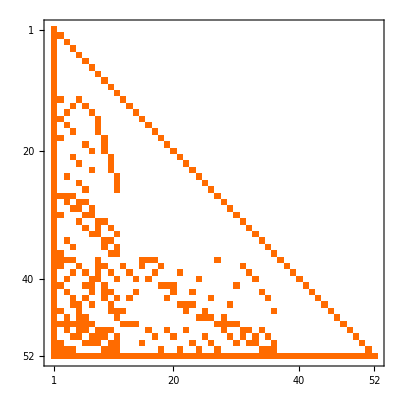

```mathematica
mat=Table[
FullBaseCoeff6[allGraphs6[k,"colofour"]],
{k,theGens6}
];MatrixPlot[mat]
```

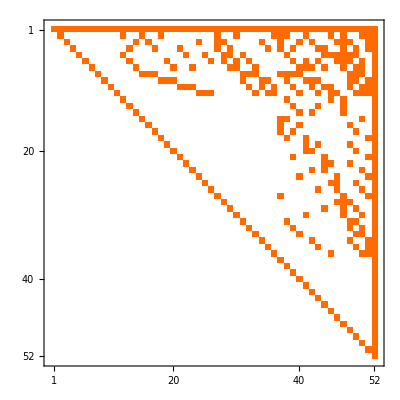

```mathematica
mat2=Table[
FullBaseCoeff6[allGraphs6[k,"colofour"]],
{k,Sort[allGraphs6NullAtomKeys,CompareSymbols[allGraphs6[#1,"colofourrealnull"],allGraphs6[#2,"colofourrealnull"]]&]}
];MatrixPlot[mat2]
```

```mathematica
mat==Transpose[mat2]
```

True

## Mobius and zeta

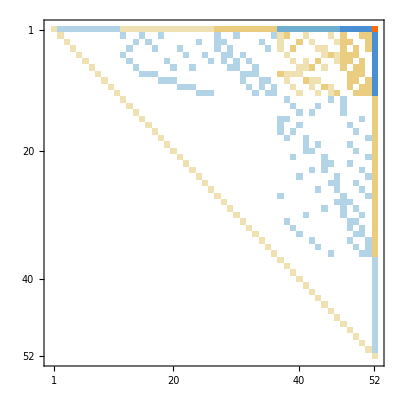

```mathematica
mob6=MobiusMatrix[allGraphs6];MatrixPlot[mob6]
```

```mathematica
zeta6=Inverse[mob6];MatrixPlot[zeta6]
```

-Graphics-

```mathematica
zeta6Transp=Transpose[zeta6];MatrixPlot[zeta6Transp]
```

-Graphics-

```mathematica
T
```

T

```mathematica
Monitor[Table[allGraphs6[k,"fullbasecoeff"]=FullBaseCoeff6[allGraphs6[k,"colofour"]],{k,Sort[Keys[allGraphs6]]}],k]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,0,0,0,1,1,0,1,1,1,0,1,0,1,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,0,1,0,0,0,1,0,1,0,0,1,1,1},1889,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
Monitor[Table[allGraphs6[k,"emptybasecoeff"]=EmptyBaseCoeff6[allGraphs6[k,"colofourrealnull"]],{k,Sort[Keys[allGraphs6]]}],k]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1889,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
Map[ShowGraph[allGraphs6,#]&,Monitor[
Table[
Select[Keys[allGraphs6],allGraphs6[#,"fullbasecoeff"]==zeta6Transp[[k]]&]//First,
{k,1,62}
],
k]]
```

```mathematica
{-Graphics-29624,-Graphics-29623,-Graphics-29616,-Graphics-29621,-Graphics-29281,-Graphics-29443,-Graphics-29497,-Graphics-9841,-Graphics-22963,-Graphics-27337,-Graphics-28796,-Graphics-29280,-Graphics-29440,-Graphics-29488,-Graphics-9840,-Graphics-9832,-Graphics-9838,-Graphics-22962,-Graphics-22882,-Graphics-22936,-Graphics-27334,-Graphics-27094,-Graphics-27310,-Graphics-28786,-Graphics-28662,-Graphics-28714,-Graphics-29611,-Graphics-29191,-Graphics-29261,-Graphics-29416,-Graphics-3037,-Graphics-7673,-Graphics-9086,-Graphics-20767,-Graphics-22231,-Graphics-26607,-Graphics-9828,-Graphics-3036,-Graphics-7670,-Graphics-9076,-Graphics-22864,-Graphics-20740,-Graphics-22160,-Graphics-27064,-Graphics-26364,-Graphics-28462,-Graphics-29160,-Graphics-760,-Graphics-2278,-Graphics-6816,-Graphics-20034,-Graphics-0}
```

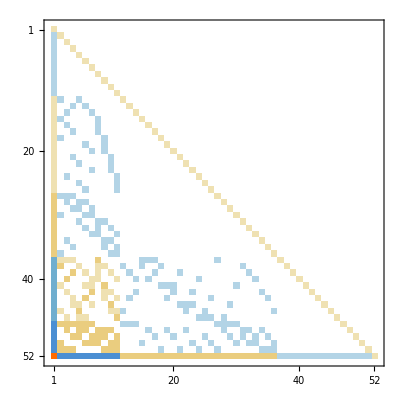

```mathematica
mob6Transp=Transpose[mob6];MatrixPlot[mob6Transp]
```

```mathematica
ZeroOne[vect_]:=Table[If[vect[[kk]]≠0,1,0],{kk,Length[vect]}]
```

```mathematica
FakeNull=Table[
Select[Keys[allGraphs6],ZeroOne[allGraphs6[#,"emptybasecoeff"]]==ZeroOne[mob6Transp[[k]]]&]//First,
{k,1,62}
]
```

```mathematica
{0,1,9,3,243,81,27,19683,6661,2187,729,244,84,36,19684,19692,19686,6662,6642,6688,2190,2430,2214,738,972,810,13,333,273,109,26487,21961,20439,8767,7293,2917,19696,26488,21964,20448,6670,8784,7374,2460,3160,1062,364,28764,27246,22708,9490,29624}
```

```mathematica
Map[Length[ListofVars[allGraphs6[#,"genfour"]]]&,FakeNull]
```

```mathematica
{1,37,37,37,37,37,37,37,37,37,37,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,17,17,17,17,17,17,17,17,17,17,13,13,13,13,13,13,13,13,13,13,6,6,6,6,6,1}
```

```mathematica
Map[Length[ListofVars[allGraphs6[#,"colofour"]]]&,FakeNull]
```

```mathematica
{62,37,37,37,37,37,37,37,37,37,37,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,17,17,17,17,17,17,17,17,17,17,13,13,13,13,13,13,13,13,13,13,6,6,6,6,6,1}
```

```mathematica
Map[Length[allGraphs6[#,"vertexsets"]]&,FakeNull]
```

```mathematica
{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
```

```mathematica
Map[EdgeCount[allGraphs6[#,"graph"]]&,FakeNull]
```

{0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,10}

```mathematica
Map[Length[ListofVars[allGraphs6[#,"colofournull"]]]&,FakeNull]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Map[Length[ListofVars[allGraphs6[#,"colofourrealnull"]]]&,FakeNull]
```

```mathematica
{1,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,6,6,6,6,6,10,10,10,10,10,10,10,10,10,10,16,16,16,16,16,62}
```

```mathematica
MatrixRank[Map[FullBaseCoeff6[allGraphs6[#,"colofour"]]&,FakeNull]]
```

```mathematica
62
```

```mathematica
Map[ShowGraph[allGraphs6,#]&,FakeNull]
```

```mathematica
{-Graphics-0,-Graphics-1,-Graphics-9,-Graphics-3,-Graphics-243,-Graphics-81,-Graphics-27,-Graphics-19683,-Graphics-6661,-Graphics-2187,-Graphics-729,-Graphics-244,-Graphics-84,-Graphics-36,-Graphics-19684,-Graphics-19692,-Graphics-19686,-Graphics-6662,-Graphics-6642,-Graphics-6688,-Graphics-2190,-Graphics-2430,-Graphics-2214,-Graphics-738,-Graphics-972,-Graphics-810,-Graphics-13,-Graphics-333,-Graphics-273,-Graphics-109,-Graphics-26487,-Graphics-21961,-Graphics-20439,-Graphics-8767,-Graphics-7293,-Graphics-2917,-Graphics-19696,-Graphics-26488,-Graphics-21964,-Graphics-20448,-Graphics-6670,-Graphics-8784,-Graphics-7374,-Graphics-2460,-Graphics-3160,-Graphics-1062,-Graphics-364,-Graphics-28764,-Graphics-27246,-Graphics-22708,-Graphics-9490,-Graphics-29624}
```

```mathematica
allGraphs6[9490,"emptybasecoeff"]
```

{1,-1,-1,-1,0,0,0,0,-1,-1,-1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,2,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,0}

```mathematica
-mob6Transp[[61]]
```

{6,-2,-2,-2,0,0,0,0,-2,-2,-2,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0}

```mathematica
allGraphs6[2214,"compwhy"]
```

The relation holds x2214== x21897(Greater) + 42390 (Greater)

```mathematica
mob6Transp[[62]]
```

{24,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1}

```mathematica
Table[
Select[Keys[allGraphs6],EmptyBaseCoeff6[allGraphs6[#,"colofourrealnull"]]==Reverse[mob6Transp[[k]]]&],
{k,1,16}
]
```

$Aborted

```mathematica
{{728},{673},{637},{697},{377},{600},{648},{},{},{},{},{},{},{},{}}
```

```mathematica
ShowGraph[allGraphs4,400]
```

-Graphics-400